```mathematica
ClearAll["Global`*"];
main="/Users/mikhailgaerlan/Box Sync/Education/UC Davis/2016-2017 Winter/PHY 250 Econophysics/Projects/Project 1/project_files";
SetDirectory[main];
$Line=0;
```

```mathematica
list=Import["Stocks_List.txt","Table"];
plots={};threemonthreturns=Range[Length[list]];twelvemonthreturns=Range[Length[list]];
For[j=1,j≤Length[list],j++,
data=Import[list[[j,1]]<>"_File.txt","Table"];
threemonthreturns[[j]]=Table[{data[[-i,1]],(data[[-i,5]]-data[[-i-21*3,5]])/data[[-i-21*3,5]]*100},{i,252*17}];
twelvemonthreturns[[j]]=Table[{data[[-i,1]],(data[[-i,5]]-data[[-i-21*12,5]])/data[[-i-21*12,5]]*100},{i,252*17}];
Print[list[[j,1]],"  ",Min[threemonthreturns[[j]]],"  ",Min[twelvemonthreturns[[j]]]];
Export[list[[j,1]]<>"_returns.png",ListLinePlot[{twelvemonthreturns[[j]],threemonthreturns[[j]]},PlotLegends->{Text[Style["12 month",FontSize->10,FontFamily->"Times"]],Text[Style["3 month",FontSize->10,FontFamily->"Times"]]},PlotTheme->"Classic",PlotRange->All,Frame->True,Axes->False,ImageSize->300,PlotLabel->list[[j,1]]<>" Twelve Month Returns",FrameLabel->{"Date","Return (%)"},BaseStyle->{FontSize->10}],ImageResolution->100];
]
```

^GSPC  -41.7706  -48.8228

^VIX  -62.0275  -72.5575

SPY  -41.8049  -48.5915

AAPL  -84.8428  -86.996

MSFT  -60.0035  -64.6996

PG  -51.0808  -51.0703

FDX  -51.6707  -67.8392

KO  -54.5095  -50.3278

GE  -69.5312  -80.2198

YHOO  -77.005  -94.0658

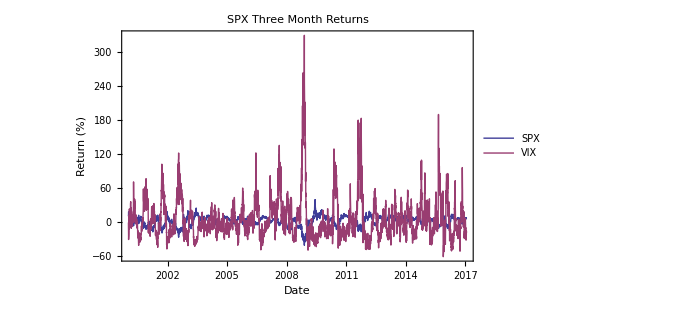

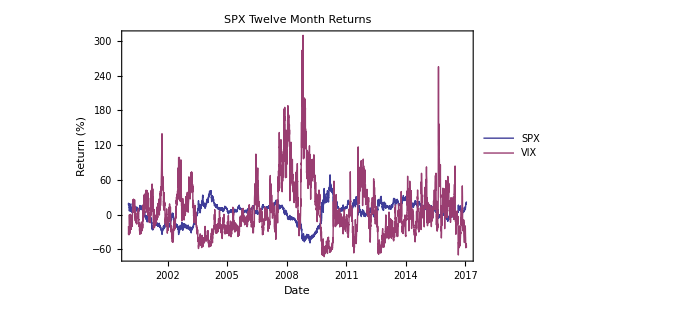

```mathematica
ListLinePlot[{threemonthreturns[[1]],threemonthreturns[[2]]},PlotLegends->{"SPX","VIX"},PlotTheme->"Classic",PlotRange->All,Frame->True,Axes->False,ImageSize->500,PlotLabel->"SPX Three Month Returns",FrameLabel->{"Date","Return (%)"}]
ListLinePlot[{twelvemonthreturns[[1]],twelvemonthreturns[[2]]},PlotLegends->{"SPX","VIX"},PlotTheme->"Classic",PlotRange->All,Frame->True,Axes->False,ImageSize->500,PlotLabel->"SPX Twelve Month Returns",FrameLabel->{"Date","Return (%)"}]
```